```mathematica
BesselProperties=CreateDocument[{
TextCell["Orthogonality and Fourier Analysis with Bessel Functions","Title",FontColor->Black],
TextCell["In the Trigg Orthogonality notebook, we discussed the general inner product determining the orthogonality of two functions, introduced in equation (1.16), before exploring the orthogonality of sine and cosine. Let's now take a look at the orthogonality of Bessel functions, given by equation (2.32). Once again, these functions do not visually appear to be perpendicular to one another. In the following example, two Bessel functions of the first kind will be shown, with n=1 in red and n=2 in green.","Text"],
ExpressionCell[Plot[{BesselJ[1,(BesselJZero[1,1]*x)],BesselJ[1,(BesselJZero[1,2]*x)]},{x,0,1},PlotStyle->{Red,Green}],"Output"],
TextCell["Let's now try graphing the integrand of equation (2.32), where m is the order of the Bessel function, n1 and n2 are the nth zeroes of the Bessel function, and a is our arbitrary starting point. The opaque blue curve represents the integrand of equation (2.32), while the red and green curves represent the individual Bessel functions, which have been initialized to the previously discussed situation with n=1 and n=2. The result of equation (2.32) is also included above the graph.","Text"],
ExpressionCell[
graph=Manipulate[Plot[{x*BesselJ[m,(BesselJZero[m,n1]*x)/a]*BesselJ[m,(BesselJZero[m,n2]*x)/a],BesselJ[1,(BesselJZero[1,1]*x)],BesselJ[1,(BesselJZero[1,2]*x)]},{x,0,a},Filling->{1->Axis},PlotLabel->Style[Framed[Integrate[x*BesselJ[m,(BesselJZero[m,n1]*x)/a]*BesselJ[m,(BesselJZero[m,n2]*x)/a],{x,0,a}]]],PlotStyle->{Blue,Directive[Red,Opacity[0.2]],Directive[Green,Opacity[0.2]]}],{{m,0},-10,10,1},{{n1,1},1,10,1},{{n2,2},1,10,1},{a,1,10,1},FrameLabel->"Bessel Functions"];
graph,"Output"
],
TextCell["Here we can clearly see that the area under the curve (the shaded area) totals to zero when we expect the functions to be orthogonal, but that it totals to some nonzero value when the functions are not orthogonal. Try out adjusting the sliders to convince yourself of these conclusions. Let's take a look next at an application of this orthogonality relationship: Fourier Analysis with Bessel Functions.","Text"],
TextCell["As discussed previously, Fourier analysis makes use of the orthogonality of a special function to 'pick out' individual terms and find their coefficients. For Bessel functions of the first kind, the Fourier expansion is introduced in equation (2.35), restated below:","Text"],
ExpressionCell[HoldForm[f[ρ]=Sum[c_mn*J[k_[m,n]*ρ],{n=1,Infinity}]],"Output"],
TextCell[
" This Fourier-Bessel series is more specific in utility than the Fourier series with sine and cosine, often being used as solutions to differential equations. To get a better sense of using Fourier analysis with Bessel functions, let's look at a few examples.","Text"],
TextCell["First, we'll try a very simple function, f(x)=1, for 0<x<1. Using the orthogonality of Bessel functions of the first kind, our coefficients will be:","Text"],
ExpressionCell[HoldForm[c_mn=((Integrate[x*1*BesselJ[m,(BesselJZero[m,n]*x)],{x,0,1}])/((1/2)*(BesselJ[(m+1),(BesselJZero[m,n])])^2))],"Output"],
TextCell["Evaluating these expressions, and plugging them into equation (2.35) gives us our Fourier-Bessel series. In the figure, the dotted red curve is our function f(x), while the blue curve is our Fourier-Bessel Series. Using the slider to increase n, you will see that adding in more terms makes our approximation more accurate.","Text"],
ExpressionCell[
topbf1 = Plot[(1),{x,0,1},PlotStyle -> {Red,Dashed,Thick}];
(*c=((Integrate[x*1*BesselJ[m,(BesselJZero[m,i]*x)],{x,0,1}])/((1^2/2)*(BesselJ[(m+1),(BesselJZero[m,i])])^2));*)
Manipulate[Show[Plot[(1),{x,0,1},PlotStyle -> {Red,Dashed,Thick}],Plot[NSum[((2^(1-m) BesselJZero[m,i]^m HypergeometricPFQ[{1+m/2},{2+m/2,1+m},-1/4 BesselJZero[m,i]^2])/((2+m) BesselJ[1+m,BesselJZero[m,i]]^2 Gamma[1+m]))*BesselJ[m,(BesselJZero[m,i]*x)],{i,n}],{x,0,1},PlotPoints->ControlActive[30,150]]],{{n,1},1,10,1},{{m,1},0,10,1}]
,"Output"],
TextCell["Note that the values for n and m are limited to smaller numbers. This is simply to make sure the expression runs more efficiently, as higher values for n and m take longer to run. As a further note, changing the n and m values for the Fourier-Bessel fit might make the displayed graph disappear or instead display an '$Aborted' message. This just means that the graph is not displayed while Mathematica finishes running calculations, so if you let it run for some time, the graph should eventually appear. If worse comes to worse, you can close and reopen the notebook. ","Text"],
TextCell["Let's now take a look at another simple function, f(x)=x (represented by the dotted red curve), for 0<x<1, while the Fourier-Bessel Series is represented by the blue curve. We find the following:","Text"],
ExpressionCell[
topbfx = Plot[(x),{x,0,1},PlotStyle -> {Red,Dashed,Thick}];
Manipulate[Show[Plot[(x),{x,0,1},PlotStyle -> {Red,Dashed,Thick}],Plot[NSum[(2^-m BesselJZero[m,i]^m Gamma[(3+m)/2] HypergeometricPFQRegularized[{(3+m)/2},{1+m,(5+m)/2},-1/4 BesselJZero[m,i]^2])/BesselJ[1+m,BesselJZero[m,i]]^2*BesselJ[m,(BesselJZero[m,i]*x)],{i,n}],{x,0,1},PlotPoints->ControlActive[30,150]]],{{n,1},1,10,1},{{m,1},0,10,1}]
,"Output"],
TextCell["Starting from this point, it is clear that we can expand these examples to match the square and sawtooth waveforms from the Trigg Fourier Series notebook.","Text"]
},
WindowTitle->"BesselProperties"]
NotebookSave[BesselProperties]
```

nvnji_shm21FrontEndObject[LinkObject["nvnji_shm", 3, 1]]21BesselProperties

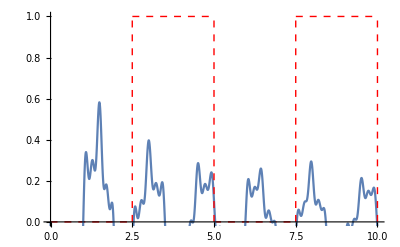

```mathematica
(*constant figure of bessel fit for sawtooth and squarewave*)
(*f(x)=(HeavisideTheta[x-2.5]-HeavisideTheta[x-5]+HeavisideTheta[x-7.5]),{x,0,10};*)
(*c=*)(*((Integrate[x*(HeavisideTheta[x-2.5]-HeavisideTheta[x-5]+HeavisideTheta[x-7.5])*BesselJ[m,(BesselJZero[m,i]*x)],{x,0,10}])/((10^2/2)*(BesselJ[(m+1),(10*BesselJZero[m,i])])^2))*)
(*the graph*)
fxsqtop = Plot[(HeavisideTheta[x-2.5]-HeavisideTheta[x-5]+HeavisideTheta[x-7.5]),{x,0,10},PlotStyle -> {Red,Dashed,Thick}];
fxsqside1 = ParametricPlot[{2.5,t},{t,0,1},PlotStyle -> {Red,Dashed,Thick}];
fxsqside2 = ParametricPlot[{5,t},{t,0,1},PlotStyle -> {Red,Dashed,Thick}];
fxsqside3 = ParametricPlot[{7.5,t},{t,0,1},PlotStyle -> {Red,Dashed,Thick}];
fxsqside4 = ParametricPlot[{10,t},{t,0,1},PlotStyle -> {Red,Dashed,Thick}];
m=1;
Show[Plot[(HeavisideTheta[x-2.5]-HeavisideTheta[x-5]+HeavisideTheta[x-7.5]),{x,0,10},PlotStyle -> {Red,Dashed,Thick}],Plot[NSum[((2 BesselJZero[m,i]^m Gamma[1+m/2] (1. 10^m ⅇ^(-0.7 m) ((1.+m) (4.+m) HypergeometricPFQ[{1.+0.5 m},{1.+m,2.+0.5 m},-25. BesselJZero[m,i]^2]+5*^-13 (2.+m) BesselJZero[m,i]^2 HypergeometricPFQ[{2.+0.5 m},{2.+m,3.+0.5 m},-25. BesselJZero[m,i]^2])-0.3 7.5^m ⅇ^(-0.7 m) ((1.+m) (4.+m) HypergeometricPFQ[{1.+0.5 m},{1.+m,2.+0.5 m},-14 BesselJZero[m,i]^2]-2.8*^-13 (2.+m) BesselJZero[m,i]^2 HypergeometricPFQ[{2.+0.5 m},{2.+m,3.+0.5 m},-14 BesselJZero[m,i]^2])-0.03125 2.5^m ⅇ^(-0.6931471805599453 m) ((1.+m) (4.+m) HypergeometricPFQ[{1.+0.5 m},{1.+m,2.+0.5 m},-1.5625 BesselJZero[m,i]^2]-3.1*^-14 (2.+m) BesselJZero[m,i]^2 HypergeometricPFQ[{2.+0.5 m},{2.+m,3.+0.5 m},-1.6 BesselJZero[m,i]^2])-0.5 (5/2)^m (1.+m) (4.+m) Gamma[2.+0.5 m] Gamma[1.+m] (1. 2^m HypergeometricPFQRegularized[{1+m/2},{2+m/2,1+m},-25 BesselJZero[m,i]^2]-0.25 HypergeometricPFQRegularized[{1+m/2},{2+m/2,1+m},-25/4 BesselJZero[m,i]^2])))/((1.+m) (4.+m) BesselJ[1+m,10 BesselJZero[m,i]]^2 Gamma[2.+0.5 m] Gamma[1.+m]))*BesselJ[m,(BesselJZero[m,i]*x)],{i,100}],{x,0,10},PlotPoints->ControlActive[30,150]],ParametricPlot[{2.5,t},{t,0,1},PlotStyle -> {Red,Dashed,Thick}],ParametricPlot[{5,t},{t,0,1},PlotStyle -> {Red,Dashed,Thick}],ParametricPlot[{7.5,t},{t,0,1},PlotStyle -> {Red,Dashed,Thick}],ParametricPlot[{10,t},{t,0,1},PlotStyle -> {Red,Dashed,Thick}]]
```

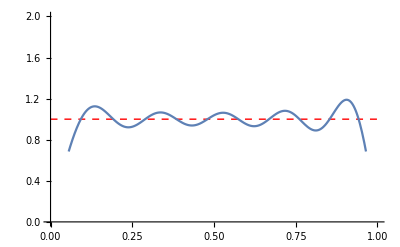

```mathematica
Show[Plot[(1),{x,0,1},PlotStyle -> {Red,Dashed,Thick}],Plot[NSum[((2^(1-1) BesselJZero[1,i]^1 HypergeometricPFQ[{1+1/2},{2+1/2,1+1},-1/4 BesselJZero[1,i]^2])/((2+1) BesselJ[1+1,BesselJZero[1,i]]^2 Gamma[1+1]))*BesselJ[1,(BesselJZero[1,i]*x)],{i,10}],{x,0,1},PlotPoints->ControlActive[30,150]]]
```

```mathematica
(*Plot[HeavisideTheta[x-2.5],{x,0,5}]*)
(*c=*)(*((Integrate[x*(HeavisideTheta[x-2.5])*BesselJ[1,(BesselJZero[1,i]*x)],{x,0,5}])/((5^2/2)*(BesselJ[(1+1),(5*BesselJZero[1,i])])^2))*)
Show[Plot[(HeavisideTheta[x-2.5]),{x,0,5},PlotStyle -> {Red,Dashed,Thick}],Plot[Sum[((2 BesselJZero[1,i] (20.8 HypergeometricPFQ[{3/2},{2,5/2},-6.25 BesselJZero[1,i]^2]-2.6 HypergeometricPFQ[{3/2},{2,5/2},-1.56 BesselJZero[1,i]^2]))/(25 BesselJ[2,5 BesselJZero[1,i]]^2))*BesselJ[1,(BesselJZero[1,i]*x)],{i,30}],{x,0,5},PlotPoints->ControlActive[30,150]],ParametricPlot[{2.5,t},{t,0,1},PlotStyle -> {Red,Dashed,Thick}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in i near {i} = {19.5271}. NIntegrate obtained -0.00971302 and 0.0140232 for the integral and error estimates.

NSum::emcon: Euler-Maclaurin sum failed to converge to requested error tolerance.

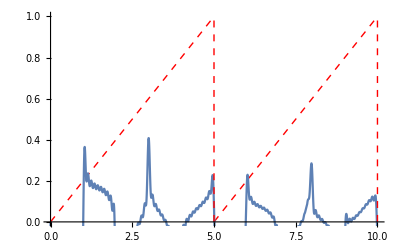

```mathematica
(*c=*)(*((Integrate[x*(x/5-HeavisideTheta[x-5])*BesselJ[1,(BesselJZero[1,i]*x)],{x,0,10}])/((10^2/2)*(BesselJ[(1+1),(10*BesselJZero[1,i])])^2))*)
Show[Plot[(x/5-HeavisideTheta[x-5]),{x,0,10},PlotStyle -> {Red,Dashed,Thick}],Plot[NSum[(((20 BesselJ[2,10 BesselJZero[1,i]])/BesselJZero[1,i]-125/6 BesselJZero[1,i] (8 HypergeometricPFQ[{3/2},{2,5/2},-25 BesselJZero[1,i]^2]-HypergeometricPFQ[{3/2},{2,5/2},-25/4 BesselJZero[1,i]^2]))/(50 BesselJ[2,10 BesselJZero[1,i]]^2))*BesselJ[1,(BesselJZero[1,i]*x)],{i,20}],{x,0,10},PlotPoints->ControlActive[30,150]],ParametricPlot[{5,t},{t,0,1},PlotStyle -> {Red,Dashed,Thick}],ParametricPlot[{10,t},{t,0,1},PlotStyle -> {Red,Dashed,Thick}]]
```